## Q1

```mathematica
Quit[]
```

```mathematica
rho=ρ[t,x,y,z]; p = P[t,x,y,z];e=En[t,x,y,z];phi = ϕ[t,x,y,z]; v={vx[t,x,y,z],vy[t,x,y,z],vz[t,x,y,z]}; F={Fx[t,x,y,z],Fy[t,x,y,z],Fz[t,x,y,z]};
```

### Energy equation for self-gravitating gas:

```mathematica
eq[1]=D[rho e + 1/2 rho phi,t]+Div[(rho e+p)v+F,{x,y,z}]==0
```

Fz^(0,0,0,1)[t,x,y,z]+(P[t,x,y,z]+En[t,x,y,z] ρ[t,x,y,z]) vz^(0,0,0,1)[t,x,y,z]+vz[t,x,y,z] (ρ[t,x,y,z] En^(0,0,0,1)[t,x,y,z]+P^(0,0,0,1)[t,x,y,z]+En[t,x,y,z] ρ^(0,0,0,1)[t,x,y,z])+Fy^(0,0,1,0)[t,x,y,z]+(P[t,x,y,z]+En[t,x,y,z] ρ[t,x,y,z]) vy^(0,0,1,0)[t,x,y,z]+vy[t,x,y,z] (ρ[t,x,y,z] En^(0,0,1,0)[t,x,y,z]+P^(0,0,1,0)[t,x,y,z]+En[t,x,y,z] ρ^(0,0,1,0)[t,x,y,z])+Fx^(0,1,0,0)[t,x,y,z]+(P[t,x,y,z]+En[t,x,y,z] ρ[t,x,y,z]) vx^(0,1,0,0)[t,x,y,z]+vx[t,x,y,z] (ρ[t,x,y,z] En^(0,1,0,0)[t,x,y,z]+P^(0,1,0,0)[t,x,y,z]+En[t,x,y,z] ρ^(0,1,0,0)[t,x,y,z])+ρ[t,x,y,z] En^(1,0,0,0)[t,x,y,z]+En[t,x,y,z] ρ^(1,0,0,0)[t,x,y,z]+1/2 ϕ[t,x,y,z] ρ^(1,0,0,0)[t,x,y,z]+1/2 ρ[t,x,y,z] ϕ^(1,0,0,0)[t,x,y,z]==0

### Energy equation (given):

```mathematica
eq[2]=D[rho e,t]+Div[(rho e+p)v,{x,y,z}]==0
```

(P[t,x,y,z]+En[t,x,y,z] ρ[t,x,y,z]) vz^(0,0,0,1)[t,x,y,z]+vz[t,x,y,z] (ρ[t,x,y,z] En^(0,0,0,1)[t,x,y,z]+P^(0,0,0,1)[t,x,y,z]+En[t,x,y,z] ρ^(0,0,0,1)[t,x,y,z])+(P[t,x,y,z]+En[t,x,y,z] ρ[t,x,y,z]) vy^(0,0,1,0)[t,x,y,z]+vy[t,x,y,z] (ρ[t,x,y,z] En^(0,0,1,0)[t,x,y,z]+P^(0,0,1,0)[t,x,y,z]+En[t,x,y,z] ρ^(0,0,1,0)[t,x,y,z])+(P[t,x,y,z]+En[t,x,y,z] ρ[t,x,y,z]) vx^(0,1,0,0)[t,x,y,z]+vx[t,x,y,z] (ρ[t,x,y,z] En^(0,1,0,0)[t,x,y,z]+P^(0,1,0,0)[t,x,y,z]+En[t,x,y,z] ρ^(0,1,0,0)[t,x,y,z])+ρ[t,x,y,z] En^(1,0,0,0)[t,x,y,z]+En[t,x,y,z] ρ^(1,0,0,0)[t,x,y,z]==0

### Subtracting the two equations:

```mathematica
eq[3]=eq[1]-eq[2]//Factor
```

-((P[t,x,y,z]+En[t,x,y,z] ρ[t,x,y,z]) vz^(0,0,0,1)[t,x,y,z]+vz[t,x,y,z] (ρ[t,x,y,z] En^(0,0,0,1)[t,x,y,z]+P^(0,0,0,1)[t,x,y,z]+En[t,x,y,z] ρ^(0,0,0,1)[t,x,y,z])+(P[t,x,y,z]+En[t,x,y,z] ρ[t,x,y,z]) vy^(0,0,1,0)[t,x,y,z]+vy[t,x,y,z] (ρ[t,x,y,z] En^(0,0,1,0)[t,x,y,z]+P^(0,0,1,0)[t,x,y,z]+En[t,x,y,z] ρ^(0,0,1,0)[t,x,y,z])+(P[t,x,y,z]+En[t,x,y,z] ρ[t,x,y,z]) vx^(0,1,0,0)[t,x,y,z]+vx[t,x,y,z] (ρ[t,x,y,z] En^(0,1,0,0)[t,x,y,z]+P^(0,1,0,0)[t,x,y,z]+En[t,x,y,z] ρ^(0,1,0,0)[t,x,y,z])+ρ[t,x,y,z] En^(1,0,0,0)[t,x,y,z]+En[t,x,y,z] ρ^(1,0,0,0)[t,x,y,z]==0)+(Fz^(0,0,0,1)[t,x,y,z]+(P[t,x,y,z]+En[t,x,y,z] ρ[t,x,y,z]) vz^(0,0,0,1)[t,x,y,z]+vz[t,x,y,z] (ρ[t,x,y,z] En^(0,0,0,1)[t,x,y,z]+P^(0,0,0,1)[t,x,y,z]+En[t,x,y,z] ρ^(0,0,0,1)[t,x,y,z])+Fy^(0,0,1,0)[t,x,y,z]+(P[t,x,y,z]+En[t,x,y,z] ρ[t,x,y,z]) vy^(0,0,1,0)[t,x,y,z]+vy[t,x,y,z] (ρ[t,x,y,z] En^(0,0,1,0)[t,x,y,z]+P^(0,0,1,0)[t,x,y,z]+En[t,x,y,z] ρ^(0,0,1,0)[t,x,y,z])+Fx^(0,1,0,0)[t,x,y,z]+(P[t,x,y,z]+En[t,x,y,z] ρ[t,x,y,z]) vx^(0,1,0,0)[t,x,y,z]+vx[t,x,y,z] (ρ[t,x,y,z] En^(0,1,0,0)[t,x,y,z]+P^(0,1,0,0)[t,x,y,z]+En[t,x,y,z] ρ^(0,1,0,0)[t,x,y,z])+ρ[t,x,y,z] En^(1,0,0,0)[t,x,y,z]+En[t,x,y,z] ρ^(1,0,0,0)[t,x,y,z]+1/2 ϕ[t,x,y,z] ρ^(1,0,0,0)[t,x,y,z]+1/2 ρ[t,x,y,z] ϕ^(1,0,0,0)[t,x,y,z]==0)

### Continuity equation:

```mathematica
s=Div[rho v,{x,y,z}]-> -D[rho,t]
```

ρ[t,x,y,z] vz^(0,0,0,1)[t,x,y,z]+vz[t,x,y,z] ρ^(0,0,0,1)[t,x,y,z]+ρ[t,x,y,z] vy^(0,0,1,0)[t,x,y,z]+vy[t,x,y,z] ρ^(0,0,1,0)[t,x,y,z]+ρ[t,x,y,z] vx^(0,1,0,0)[t,x,y,z]+vx[t,x,y,z] ρ^(0,1,0,0)[t,x,y,z]→-ρ^(1,0,0,0)[t,x,y,z]

```mathematica
eq[3]==eq[3]/.s
```

True

### Poisson’s equation

```mathematica
eq[4]=Laplacian[phi,{x,y,z}]==4 Pi G rho
```

ϕ^(0,0,0,2)[t,x,y,z]+ϕ^(0,0,2,0)[t,x,y,z]+ϕ^(0,2,0,0)[t,x,y,z]==4 G π ρ[t,x,y,z]

```mathematica
Solve[Table[eq[i],{i,4}],F,{phi,rho,v,G,t,x,y,z}]
```

Solve::ivar: {vx[t,x,y,z],vy[t,x,y,z],vz[t,x,y,z]} is not a valid variable.

Solve[{Fz^(0,0,0,1)[t,x,y,z]+(P[t,x,y,z]+En[t,x,y,z] ρ[t,x,y,z]) vz^(0,0,0,1)[t,x,y,z]+vz[t,x,y,z] (ρ[t,x,y,z] En^(0,0,0,1)[t,x,y,z]+P^(0,0,0,1)[t,x,y,z]+En[t,x,y,z] ρ^(0,0,0,1)[t,x,y,z])+Fy^(0,0,1,0)[t,x,y,z]+(P[t,x,y,z]+En[t,x,y,z] ρ[t,x,y,z]) vy^(0,0,1,0)[t,x,y,z]+vy[t,x,y,z] (ρ[t,x,y,z] En^(0,0,1,0)[t,x,y,z]+P^(0,0,1,0)[t,x,y,z]+En[t,x,y,z] ρ^(0,0,1,0)[t,x,y,z])+Fx^(0,1,0,0)[t,x,y,z]+(P[t,x,y,z]+En[t,x,y,z] ρ[t,x,y,z]) vx^(0,1,0,0)[t,x,y,z]+vx[t,x,y,z] (ρ[t,x,y,z] En^(0,1,0,0)[t,x,y,z]+P^(0,1,0,0)[t,x,y,z]+En[t,x,y,z] ρ^(0,1,0,0)[t,x,y,z])+ρ[t,x,y,z] En^(1,0,0,0)[t,x,y,z]+En[t,x,y,z] ρ^(1,0,0,0)[t,x,y,z]==0,(P[t,x,y,z]+En[t,x,y,z] ρ[t,x,y,z]) vz^(0,0,0,1)[t,x,y,z]+vz[t,x,y,z] (ρ[t,x,y,z] En^(0,0,0,1)[t,x,y,z]+P^(0,0,0,1)[t,x,y,z]+En[t,x,y,z] ρ^(0,0,0,1)[t,x,y,z])+(P[t,x,y,z]+En[t,x,y,z] ρ[t,x,y,z]) vy^(0,0,1,0)[t,x,y,z]+vy[t,x,y,z] (ρ[t,x,y,z] En^(0,0,1,0)[t,x,y,z]+P^(0,0,1,0)[t,x,y,z]+En[t,x,y,z] ρ^(0,0,1,0)[t,x,y,z])+(P[t,x,y,z]+En[t,x,y,z] ρ[t,x,y,z]) vx^(0,1,0,0)[t,x,y,z]+vx[t,x,y,z] (ρ[t,x,y,z] En^(0,1,0,0)[t,x,y,z]+P^(0,1,0,0)[t,x,y,z]+En[t,x,y,z] ρ^(0,1,0,0)[t,x,y,z])+ρ[t,x,y,z] En^(1,0,0,0)[t,x,y,z]+En[t,x,y,z] ρ^(1,0,0,0)[t,x,y,z]==0,ρ[t,x,y,z] vz^(0,0,0,1)[t,x,y,z]+vz[t,x,y,z] ρ^(0,0,0,1)[t,x,y,z]+ρ[t,x,y,z] vy^(0,0,1,0)[t,x,y,z]+vy[t,x,y,z] ρ^(0,0,1,0)[t,x,y,z]+ρ[t,x,y,z] vx^(0,1,0,0)[t,x,y,z]+vx[t,x,y,z] ρ^(0,1,0,0)[t,x,y,z]+ρ^(1,0,0,0)[t,x,y,z]==0,ϕ^(0,0,0,2)[t,x,y,z]+ϕ^(0,0,2,0)[t,x,y,z]+ϕ^(0,2,0,0)[t,x,y,z]==4 G π ρ[t,x,y,z]},{Fx[t,x,y,z],Fy[t,x,y,z],Fz[t,x,y,z]},{ϕ[t,x,y,z],ρ[t,x,y,z],{vx[t,x,y,z],vy[t,x,y,z],vz[t,x,y,z]},G,t,x,y,z}]

```mathematica
temp=Sort[EntityValue[#,{"LifeExpectancy","Name"}]&/@CountryData[]]
```

{{Missing[NotAvailable],Christmas Island},{Missing[NotAvailable],Cocos Keeling Islands},{Missing[NotAvailable],Falkland Islands},{Missing[NotAvailable],Niue},{Missing[NotAvailable],Norfolk Island},{Missing[NotAvailable],Pitcairn Islands},{Missing[NotAvailable],Sint Maarten},{Missing[NotAvailable],Svalbard},{Missing[NotAvailable],Tokelau},{Missing[NotAvailable],Vatican City},{45.561 yr,Sierra Leone},{47.572 yr,Botswana},{49. yr,Swaziland},{49.446 yr,Lesotho},{49.963 yr,Democratic Republic of the Congo},{50.179 yr,Central African Republic},{50.25 yr,Mozambique},{51.182 yr,Chad},{51.899 yr,Angola},{52.506 yr,Nigeria},{53.062 yr,Equatorial Guinea},{54.104 yr,Burundi},{54.15 yr,Republic of the Congo},{54.291 yr,Guinea-Bissau},{55.032 yr,Mali},{55.05 yr,Somalia},{55.065 yr,Cameroon},{55.264 yr,South Sudan},{55.311 yr,Malawi},{55.45 yr,Ivory Coast},{56.112 yr,Guinea},{56.344 yr,Burkina Faso},{56.537 yr,Togo},{56.916 yr,South Africa},{58.105 yr,Zambia},{58.409 yr,Niger},{58.818 yr,Gambia},{59.209 yr,Uganda},{59.33 yr,Benin},{59.871 yr,Zimbabwe},{60.556 yr,Liberia},{60.874 yr,Comoros},{60.947 yr,Afghanistan},{61.132 yr,Ghana},{61.53 yr,Tanzania},{61.55 yr,Mauritania},{61.716 yr,Kenya},{61.801 yr,Djibouti},{62.055 yr,Sudan},{62.421 yr,Papua New Guinea},{62.852 yr,Eritrea},{63.102 yr,Haiti},{63.112 yr,Yemen},{63.451 yr,Senegal},{63.48 yr,Gabon},{63.635 yr,Ethiopia},{63.81 yr,North Korea},{64.066 yr,Rwanda},{64.2 yr,Nauru},{64.483 yr,Namibia},{64.723 yr,Madagascar},{65.176 yr,Myanmar},{65.452 yr,Turkmenistan},{66.295 yr,Guyana},{66.337 yr,São Tomé and Príncipe},{66.414 yr,India},{66.536 yr,Kazakhstan},{66.57 yr,Pakistan},{67.248 yr,Tajikistan},{67.26 yr,Bolivia},{67.27 yr,East Timor},{67.503 yr,Mongolia},{67.533 yr,Kyrgyzstan},{67.675 yr,Solomon Islands},{67.764 yr,Western Sahara},{67.979 yr,Russia},{68.241 yr,Uzbekistan},{68.294 yr,Bhutan},{68.309 yr,Laos},{68.41 yr,Nepal},{68.525 yr,Ukraine},{68.703 yr,Philippines},{68.899 yr,Moldova},{68.905 yr,Kiribati},{69.29 yr,Tuvalu},{69.419 yr,Iraq},{69.81 yr,Fiji},{69.865 yr,Trinidad and Tobago},{69.928 yr,Belarus},{70.07 yr,Greenland},{70.657 yr,Bangladesh},{70.753 yr,Azerbaijan},{70.833 yr,Indonesia},{70.941 yr,Morocco},{71. yr,Algeria},{71.019 yr,Suriname},{71.157 yr,Egypt},{71.19 yr,Marshall Islands},{71.22 yr,Palau},{71.626 yr,Vanuatu},{71.916 yr,Cambodia},{72.099 yr,Guatemala},{72.11 yr,Lithuania},{72.15 yr,Latvia},{72.259 yr,Paraguay},{72.488 yr,Saint Vincent and the Grenadines},{72.599 yr,El Salvador},{72.673 yr,Tonga},{72.76 yr,Montserrat},{72.768 yr,Grenada},{73.156 yr,Samoa},{73.187 yr,Seychelles},{73.2 yr,Saint Kitts and Nevis},{73.402 yr,Dominican Republic},{73.42 yr,Gaza Strip},{73.525 yr,Jamaica},{73.549 yr,Bulgaria},{73.613 yr,Mauritius},{73.72 yr,American Samoa},{73.799 yr,Micronesia},{73.817 yr,Honduras},{73.831 yr,Romania},{73.854 yr,Jordan},{73.882 yr,Belize},{73.937 yr,Brazil},{74.038 yr,Colombia},{74.048 yr,Iran},{74.059 yr,Serbia},{74.22 yr,Cook Islands},{74.288 yr,Kuwait},{74.293 yr,Sri Lanka},{74.301 yr,Georgia},{74.401 yr,Thailand},{74.441 yr,Estonia},{74.54 yr,West Bank},{74.553 yr,Syria},{74.561 yr,Armenia},{74.62 yr,Hungary},{74.633 yr,Venezuela},{74.804 yr,Saint Lucia},{74.821 yr,Montenegro},{74.826 yr,Peru},{74.839 yr,Nicaragua},{75.017 yr,Malaysia},{75.093 yr,Cape Verde},{75.198 yr,Macedonia},{75.237 yr,Bahamas},{75.259 yr,Turkey},{75.325 yr,Libya},{75.331 yr,China},{75.37 yr,Barbados},{75.397 yr,Slovakia},{75.42 yr,Turks and Caicos Islands},{75.455 yr,Aruba},{75.479 yr,Saudi Arabia},{75.55 yr,Dominica},{75.873 yr,Tunisia},{75.945 yr,Vietnam},{75.954 yr,Antigua and Barbuda},{76.257 yr,French Polynesia},{76.305 yr,Argentina},{76.306 yr,New Caledonia},{76.37 yr,Bosnia and Herzegovina},{76.408 yr,Poland},{76.471 yr,Ecuador},{76.552 yr,Oman},{76.608 yr,Bahrain},{76.7 yr,Northern Mariana Islands},{76.841 yr,United Arab Emirates},{77.048 yr,Croatia},{77.121 yr,French Guiana},{77.138 yr,Curacao},{77.23 yr,Uruguay},{77.26 yr,British Virgin Islands},{77.392 yr,Albania},{77.501 yr,Mexico},{77.53 yr,Kosovo},{77.556 yr,Panama},{77.69 yr,Czech Republic},{77.919 yr,Maldives},{77.96 yr,Taiwan},{78.2 yr,Wallis and Futuna Islands},{78.369 yr,Qatar},{78.44 yr,Saint Helena, Ascension and Tristan da Cunha},{78.547 yr,Brunei},{78.72 yr,South Korea},{78.82 yr,Isle of Man},{78.854 yr,Guam},{78.864 yr,Puerto Rico},{78.941 yr,United States},{79.07 yr,Saint Pierre and Miquelon},{79.19 yr,Mayotte},{79.262 yr,Cuba},{79.388 yr,Denmark},{79.44 yr,Faroe Islands},{79.591 yr,Slovenia},{79.646 yr,Réunion},{79.75 yr,Jersey},{79.75 yr,Malta},{79.841 yr,Cyprus},{79.93 yr,Costa Rica},{79.945 yr,Portugal},{79.955 yr,Chile},{80.007 yr,Lebanon},{80.06 yr,Liechtenstein},{80.09 yr,Monaco},{80.152 yr,United States Virgin Islands},{80.19 yr,Gibraltar},{80.43 yr,Bermuda},{80.44 yr,Cayman Islands},{80.535 yr,Finland},{80.547 yr,Luxembourg},{80.547 yr,United Kingdom},{80.548 yr,Belgium},{80.65 yr,Anguilla},{80.707 yr,Ireland},{80.743 yr,Germany},{80.77 yr,Greece},{80.77 yr,Guernsey},{80.947 yr,Guadeloupe},{81.038 yr,Netherlands},{81.132 yr,New Zealand},{81.137 yr,Austria},{81.41 yr,Martinique},{81.482 yr,Canada},{81.503 yr,Norway},{81.801 yr,Israel},{81.81 yr,France},{81.818 yr,Sweden},{81.86 yr,Hong Kong},{81.97 yr,San Marino},{82.086 yr,Iceland},{82.1 yr,Spain},{82.322 yr,Singapore},{82.385 yr,Italy},{82.496 yr,Australia},{82.51 yr,Andorra},{82.604 yr,Switzerland},{83.58 yr,Japan},{84.36 yr,Macau}}

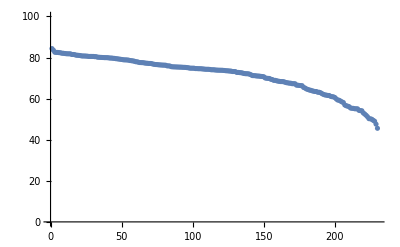

```mathematica
ListPlot[Reverse@Select[temp,!#[[1]][[0]]===Missing&][[All,1]],PlotRange->{0,100}]
```

```mathematica
a[[0]]==Missing
```

Symbol==Missing